```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

```mathematica
<<NDSolve`FEM`
```

## Importing data

```mathematica
(*numerical solution, flag == 0,
 exact solution, flag == 1 and 
error flag == 2
error velocity space flag == 3
fe index distribution flag == 4
convergence table flag == 5*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["../",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 3,
filename=StringJoin["../",outputdir,"/solution/error_velocity_space",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 4,
filename=StringJoin["../",outputdir,"/solution/fe_index",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 5,
filename=StringJoin["../",outputdir,"/convergence_tables/convergence_table",refinetype,"degree_",ToString[p]]
];

Print[Style["Reading Data from...",FontColor->Black]];
Print[Style[ToString[filename],FontColor->Green]];
result = Import[filename,"Table"][[2;;-1,All]]
]
```

## IDs for different variables

```mathematica
(*we declare the IDs for different variables, this will help us with plotting*)
DevelopVariableID[dim_]:=Module[{},

Which[dim == 2,
IDRho = 3;
IDvx = 4;
IDvy = 5;
IDtheta = 6;
IDsigmaxx = 7;
IDsigmaxy = 8;
IDsigmayy = 9;
IDqx = 10;
IDqy = 11;,
dim == 3,
IDRho = 4;
IDvx = 5;
IDvy = 6;
IDvz = 7;
IDtheta = 8;
IDsigmaxx = 9;
IDsigmaxy = 10;
IDsigmaxz = 11;
IDsigmayy = 12;
IDsigmayz = 13;
IDqx = 14;
IDqy = 15;
IDqz = 16;
];]
```

## Mapping to Primitive variables

```mathematica
(*we change the numerical solution obtained to the primitive variables.*)
ConvToPrim[sol_,dim_]:=Module[{factorθ,factorσ,factorq,trialsol},

trialsol = sol;
factorθ = -√(2/3);
factorσ = √2;
factorq = -√(5/2);
Which[dim == 2,
trialsol⟦All,IDtheta⟧ =factorθ * sol⟦All,IDtheta⟧;
trialsol⟦All,{IDqx,IDqy}⟧ =factorq*sol⟦All,{IDqx,IDqy}⟧;
trialsol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmayy}⟧=factorσ*sol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmayy}⟧;,
dim == 3,
trialsol⟦All,IDtheta⟧ =factorθ * sol⟦All,IDtheta⟧;
trialsol⟦All,{IDqx,IDqy,IDqz}⟧ =factorq*sol⟦All,{IDqx,IDqy,IDqz}⟧;
trialsol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmaxz,IDsigmayy,IDsigmayz}⟧=factorσ*sol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmaxz,IDsigmayy,IDsigmayz}⟧;
];


trialsol
]
```

## Plotting Help

### Reading A mesh

```mathematica
(*In the following function we read the gmsh file*)
ReadMeshFile[filename_]:=Import[filename,"Table"];

(*In the following function we extract the coordinates for the vertices*)
ExtractVertices[mesh_,dim_]:=Module[{nVerts,verts,offset},
(*offset from the gmsh *)
offset = 5;

(*total number of vertices in the mesh*)
nVerts = mesh⟦offset⟧⟦1⟧;

(*vertices of the mesh*)
verts = mesh⟦offset+1;;offset+nVerts,All⟧;

(*now we only extract the coordinates and not the ID of the vertex*)
verts⟦All,Range[2,dim+1,1]⟧
]

(*In the following function we extract the elements*)
ExtractElements[mesh_,dim_]:=Module[{nElm,Elm,beginElm,beginQuads,offset},
(*location where the elements begin*)
beginElm = Position[mesh,"$Elements"]⟦1,1⟧;

(*We start fron the location where the description of the mesh starts*)
Elm=mesh⟦(beginElm+2);;-2,All⟧;

(*3 Is the iD for quads and 5 is the ID for Hexahedrons*)

Which[dim==2,
beginQuads=Flatten[Position[Elm⟦All,2⟧,3]]⟦1⟧;,
dim == 3,
beginQuads=Flatten[Position[Elm⟦All,2⟧,5]]⟦1⟧;];

(*from begin quads to -2 because the last element in $EndElements*)
Elm = Elm⟦beginQuads;;-1,6;;-1⟧;

Elm
]

(*In the following routine we check the mesh which we have read from the file*)
CheckElms[Elms_,nVerts_]:=Module[{},

(*We check whether all the vertices have been included or not in the connectivity data*)

If[Norm[DeleteDuplicates[Sort[Flatten[Elms]]]-Range[1,nVerts]]==0,Print[Style["Correct Mesh",FontColor->Green]],Print[Style["InCorrect Mesh",FontColor->Red]]]
];


CreateMesh[mesh_,dim_]:=Module[{Verts,Elms,OrderedVerts,nVerts,finalMesh},

Verts = ExtractVertices[mesh,dim];
nVerts = Length[Verts];
Elms = ExtractElements[mesh,dim];

CheckElms[Elms,nVerts];

Which[dim == 2,finalMesh = ToElementMesh["Coordinates"->Verts,"MeshElements"->{QuadElement[Elms]},"MeshOrder"->1];,
dim == 3,
finalMesh = ToElementMesh["Coordinates"->Verts,"MeshElements"->{HexahedronElement[Elms]},"MeshOrder"->1];];


finalMesh
]
```

### Interpolation

```mathematica
InterpolateSolution[solution_,ID_,dim_]:=Module[{Data},

Data = Table[{solution⟦ii,Range[1,dim,1]⟧,solution⟦ii,ID⟧},{ii,1,Length[solution]}];

Data = DeleteDuplicatesBy[Data,First];

Data=Interpolation[Data,InterpolationOrder->1];

Data
]
```

## Flow Over Cylinder

### Create Mesh

```mathematica
Data = ReadMeshFile["../Meshes/Box_Cylinder/box_cylinder.msh"];
DomainMesh = CreateMesh[Data,3];
```

Correct Mesh

```mathematica
MeshPlot=DomainMesh["Wireframe"["MeshElementStyle"->EdgeForm[{Thin,Black}],PlotRange->{All,All},ImageSize->600]]
```

-Graphics3D-

### Read Data

```mathematica
ndof=61440;
foldername = "/Tests/build/output_N6_box_cylinder_inflow_3D_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
```

Reading Data from...

..//Tests/build/output_N6_box_cylinder_inflow_3D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_61440

```mathematica
DevelopVariableID[3];
numsol = ConvToPrim[numsol,3];
{ρ3D,vx3D,vy3D,vz3D,theta3D,sigmayz3D,sigmaxx3D,sigmayy3D,qz3D} = {InterpolateSolution[numsol,IDRho,3],InterpolateSolution[numsol,IDvx,3],InterpolateSolution[numsol,IDvy,3],InterpolateSolution[numsol,IDvz,3],InterpolateSolution[numsol,IDtheta,3],InterpolateSolution[numsol,IDsigmayz,3],InterpolateSolution[numsol,IDsigmaxx,3],InterpolateSolution[numsol,IDsigmayy,3],InterpolateSolution[numsol,IDqz,3]};
```

### 2D Results for Comparison

```mathematica
Data = ReadMeshFile["../Meshes/Box_Cylinder/box_cylinder_2D.msh"];
DomainMesh = CreateMesh[Data,2];
```

Correct Mesh

```mathematica
ndof=5512;
foldername = "/Tests/build/output_N6_box_cylinder_inflow_2D_Kn0p1";
numsol2D=importdata[ndof,1,"_global_",0,foldername];
```

Reading Data from...

..//Tests/build/output_N6_box_cylinder_inflow_2D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_5512

```mathematica
DevelopVariableID[2];
numsol2D = ConvToPrim[numsol2D,2];
{ρ2D,vx2D,vy2D,theta2D,sigmaxx2D,sigmayy2D} = {InterpolateSolution[numsol2D,IDRho,2],InterpolateSolution[numsol2D,IDvx,2],InterpolateSolution[numsol2D,IDvy,2],InterpolateSolution[numsol2D,IDtheta,2],InterpolateSolution[numsol,IDsigmaxx,2],InterpolateSolution[numsol,IDsigmayy,2]};
```

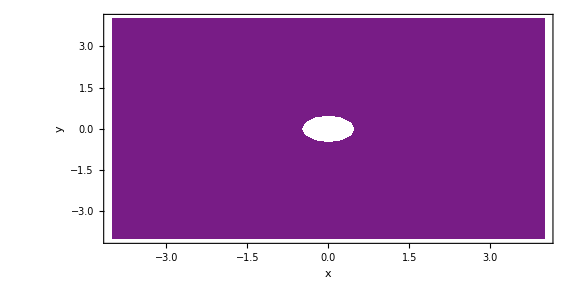

```mathematica
PlotContour[qz3D[x,y,1.5],MeshRegion[DomainMesh],2,{{-4,4},{-4,4}}]
```

```mathematica
qz3D[1,1,1.5]
```

0.

```mathematica
NIntegrate[Abs[vx2D[x,y]],{x,y}∈MeshRegion[DomainMesh]]
```

19.2276

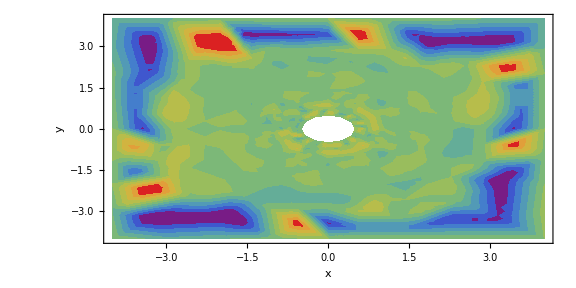

```mathematica
PlotContour[vz3D[x,y,5.0],MeshRegion[DomainMesh],2,{{-4,4},{-4,4}}]
```

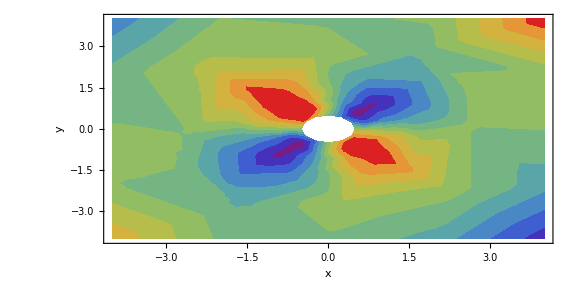

```mathematica
PlotContour[vy2D[x,y],MeshRegion[DomainMesh],2,{{-4,4},{-4,4}}]
```